# Internal State

Mathematica 8.0 Initializations

```mathematica
Off[General::"spell"];
Off[General::"spell1"];

Needs["Units`"];

SetOptions[ListAnimate, AnimationRepetitions -> 4];
SetOptions[Animate, AnimationRepetitions -> 4];
```

```mathematica
CMView={2.7,1.6,1.2};
```

#### Vector Drawer

```mathematica
(* :Date:  Copyright 1993-2007, Math Everywhere, Inc. 
*)
(*
Original Conception to create a vector drawer is due to Bill Davis.
Current code is by Bruce Carpenter.
*)
(*  :Drawbacks:  Since the vectors are drawn out of 
     context, the shapes of the arrowheads are only 
     correct with AspectRatio set to Automatic.
*)
```

```mathematica
BeginPackage["Vector3D`"];
```

```mathematica
Axes3D::usage="Axes3D[a, b] creates a Graphics3D object of cartesian axes with x, y, and z running from -a/3 to a, and with axes labels b units beyond the tips of the axes.  Axes3D[a] is Axes3D[a, a/8].";
Perpend::usage="Perpend[a] returns a unit vector which is perpendicular to the vector a.";
Vector::usage="Vector[a] produces a 2 or 3 dimensional vector from the origin to a. Arrow[a, Tail → tail] gives a vector from tail to a.";
CandMArrow::usage="CandMArrow[a, b] gives a 2D or 3D arrow from a to b.";
VectorHead::usage="VectorHead[a, vec] produces an arrowhead with its tip placed at the point a, pointing in the direction of the vector vec.";
Tail::usage="Tail → point puts the tail of the vector at point.";
Aperture::usage="Aperture is the ratio of the radius of the base to the length of the head of a vector.";
TipSize::usage="TipSize specifies an absolute size for the inner tip length of the head of a vector.";
TipRatio::usage="TipRatio is the ratio of the inner length of the arrowhead to the length of the shaft of a vector.";
HeadRatio::usage="HeadRatio is the ratio of the outer length of the arrowhead to the length of the shaft of a vector.";
HeadSize::usage="HeadSize specifies an absolute size for the head of a vector.";
ScaleFactor::usage="ScaleFactor specifies the amount to scale a vector in length and may be either a number or a pure function.";
ZeroVectorPointSize::usage="ZeroVectorPointSize is the size of the point used to represent a zero vector.";
Options[Vector]=Options[CandMArrow]=Options[VectorHead]={HeadRatio->0.18,TipRatio->0.14,Aperture->0.3,ScaleFactor->1,HeadType->Polygon,ShaftQ->True,EdgesQ->True,VectorColor->RGBColor[0,0,1],ShaftWidth->0.005,ZeroVectorPointSize->0.01};
Begin["`Private`"];
SetOptions[ParametricPlot,AspectRatio->Automatic];
SetOptions[Plot,AspectRatio->Automatic];
SetOptions[Graphics,AspectRatio->Automatic];
Axes3D[u_,v_]:=Graphics3D[{{Blue,Line[{{-u/3,0,0},{u,0,0}}]},Text["x",{u+v,0,0}],{Blue,Line[{{0,-u/3,0},{0,u,0}}]},Text["y",{0,u+v,0}],{Blue,Line[{{0,0,-u/3},{0,0,u}}]},Text["z",{0,0,u+v}]}];
Axes3D[u_]:=Axes3D[u,u/8];
Perpend[a_?VectorQ]:=Normalize[{a⟦2⟧,-a⟦1⟧}]/;Length[a]==2;
Perpend[a_?VectorQ]:=Normalize[If[a⟦1⟧==0,{1,0,0},{a⟦2⟧,-a⟦1⟧,0}]]/;Length[a]==3;
Base3D=Table[{Cos[(2 k π)/8.],Sin[(2 k π)/8.]},{k,0,8}];
CandMArrow[from_?VectorQ,to_?VectorQ,opts___]:=Module[{sq,sw,ht,hs,hr,tr,ap,sf,vc,zvps,diff=to-from,tip},{sq,sw,ht,hs,hr,ts,tr,ap,sf,vc,zvps}={ShaftQ,ShaftWidth,HeadType,HeadSize,HeadRatio,TipSize,TipRatio,Aperture,ScaleFactor,VectorColor,ZeroVectorPointSize}/.{opts}/.Options[Vector];If[from==to,Return[Graphics[{PointSize[zvps],vc,Point[from]}]]];diff=If[NumberQ[N[sf]],sf diff,sf[diff]];tip=from+diff;If[NumberQ[hs],hr=hs/Norm[diff];tr=0.75 hr];If[NumberQ[ts],tr=ts/Norm[diff]];Graphics[{If[sq,{vc,Thickness[sw],Line[{from,tip-tr diff}]},{}],With[{trans=ap hr Norm[diff] Perpend[diff]},{vc,Thickness[sw],ht[{tip,tip-hr diff+trans,tip-tr diff,tip-hr diff-trans,tip}]}]}]]/;Length[from]==Length[to]==2
CandMArrow[from_?VectorQ,to_?VectorQ,opts___]:=Module[{sq,eq,sw,hs,hr,tr,ap,sf,vc,zvps,diff=to-from,tip},{sq,eq,sw,hs,hr,ap,sf,vc,zvps}={ShaftQ,EdgesQ,ShaftWidth,HeadSize,HeadRatio,Aperture,ScaleFactor,VectorColor,ZeroVectorPointSize}/.{opts}/.Options[Vector];If[from==to,Return[Graphics3D[{PointSize[zvps],vc,Point[from]}]]];diff=If[NumberQ[N[sf]],sf diff,sf[diff]];tip=from+diff;If[NumberQ[hs],hr=hs/Norm[diff]];tr=hr/2;Graphics3D[{If[sq,{vc,Thickness[sw],Line[{from,tip-tr diff}]},{}],If[eq,{},EdgeForm[]],{SurfaceColor[vc],With[{temp=Perpend[diff]},(Polygon[Append[#1,tip]]&)/@Partition[(tip-hr diff+#1&)/@((ap hr Norm[diff] Base3D).{temp,Normalize[temp×diff]}),2,1]]}}]]/;Length[from]==Length[to]==3
Vector[a_,Tail->b_,opts___]:=CandMArrow[b,a+b,opts]
Vector[a_,opts___]:=CandMArrow[Table[0,{Length[a]}],a,opts]
VectorHead[a_,b_,opts___]:=CandMArrow[a-b,a,ShaftQ->False,opts];
End[];
EndPackage[];
```

```mathematica
Graphics`Colors`GosiaGreen=RGBColor[0, 0.392187, 0];
```

#### ThreeAxes[u,v]

```mathematica
ThreeAxes[u_,v_]:=Graphics3D[{{Blue,Line[{{-u,0,0},{u,0,0}}]},Text["x",{u+v,0,0}],{Blue,Line[{{0,-u,0},{0,u,0}}]},Text["y",{0,u+v,0}],{Blue,Line[{{0,0,0},{0,0,u}}]},Text["z",{0,0,u+v}]}];
ThreeAxes[u_]:=ThreeAxes[u,u/8];
ThreeAxes::"usage"="ThreeAxes[a,b] makes a standard cartesian axis graphics object with x, y, and z running from -a to a, and with axis labels b units beyond the tips of the axes.  ThreeAxes[a] is ThreeAxes[a,a/8].";
```

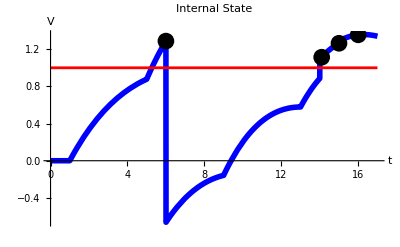

```mathematica
Clear[a,b,c,d,e,f,g,h,state,x];
a[x_]=0;
b[x_]=((x-1)/7)*2.718^(1-((x-1)/7));
c[x_]=b[x]+((x-5)/7)*2.718^(1-((x-5)/7));
d[x_]=c[x]-2*2.718^((x-8)/80);
e[x_]=d[x]+ ((x-9)/7)*2.718^(1-((x-9)/7));
f[x_]=e[x]+((x-13)/7)*2.718^(1-((x-13)/7));
g[x_]=f[x] +2*2.718^((x-8)/80)-2*2.718^((x-16)/80);
h[x_]=g[x]+2*2.718^((x-16)/80)-2*2.718^((x-17)/80);
y[x_] = 1;
state[x_]:=a[x]/;x≤1;
state[x_]:=b[x]/;x≤5;
state[x_]:=c[x]/;x≤6;
state[x_]:=d[x]/;x≤9;
state[x_]:=e[x]/;x≤13;
state[x_]:=f[x]/;x≤14;
state[x_]:=g[x]/;x≤15;
state[x_]:=h[x]/;x≤17;
stateplot=Plot[{state[x],y[x]},{x,0,17},PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.005]}},AspectRatio->1/GoldenRatio,
AxesLabel->{"t","V"},
Epilog->{{PointSize[0.03],Point[{6,state[6]}]}, {PointSize[0.03],Point[{14.1,state[14.1]}]}, {PointSize[0.03],Point[{15,state[15]}]}, {PointSize[0.03],Point[{16,state[16]}]}},
PlotLabel->"Internal State"]
```

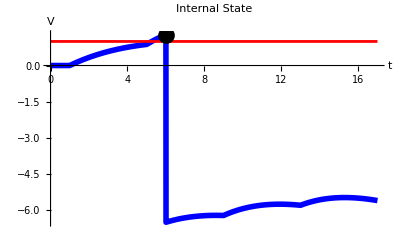

```mathematica
Clear[a,b,c,d,e,f,g,h,state,x];
a[x_]=0;
b[x_]=((x-1)/7)*2.718^(1-((x-1)/7));
c[x_]=b[x]+((x-5)/7)*2.718^(1-((x-5)/7));
d[x_]=c[x]-2*2.718^((x-8)/80)*4;
e[x_]=d[x]+ ((x-9)/7)*2.718^(1-((x-9)/7));
f[x_]=e[x]+((x-13)/7)*2.718^(1-((x-13)/7));
y[x_] = 1;
state[x_]:=a[x]/;x≤1;
state[x_]:=b[x]/;x≤5;
state[x_]:=c[x]/;x≤6;
state[x_]:=d[x]/;x≤9;
state[x_]:=e[x]/;x≤13;
state[x_]:=f[x]/;x≤17;
stateplot=Plot[{state[x],y[x]},{x,0,17},PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.005]}},AspectRatio->1/GoldenRatio,
AxesLabel->{"t","V"},
Epilog->{{PointSize[0.03],Point[{6,state[6]}]}},
PlotLabel->"Internal State"]
```